```mathematica
Reduce[bottom==2top&&0<top<(2 bottom)/3,top]
```

bottom>0&&top==bottom/2

```mathematica
Reduce[bottom==2top,top]
```

top==bottom/2

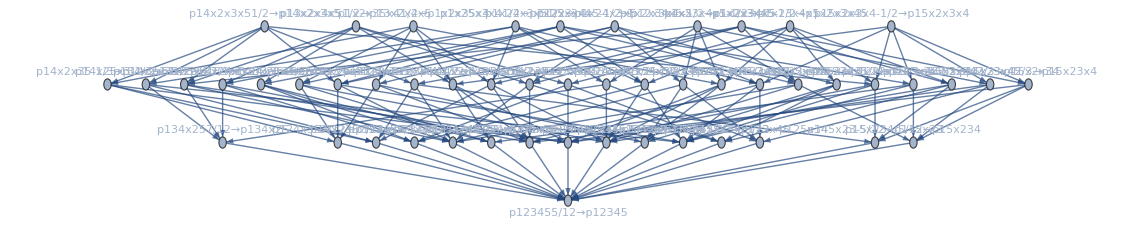

```mathematica
GenGraph[Simplify[Total[Table[allGraphs5[k,"colofournull"],{k,alfa1s}]]]]
```

```mathematica
Simplify[Total[Table[allGraphs5[k,"colofournull"],{k,alfa1s}]]==0]
```

5 p12345+6 p123x4x5+7 p124x35+6 p125x3x4+8 p12x34x5+8 p12x3x45+7 p134x25+7 p135x24+7 p13x245+6 p13x2x4x5+6 p145x2x3+7 p14x235+6 p14x2x3x5+8 p15x23x4+8 p15x2x34+6 p1x234x5+8 p1x23x45+6 p1x24x3x5+6 p1x25x3x4+6 p1x2x345+6 p1x2x35x4==3 p1234x5+3 p1235x4+5 p123x45+3 p1245x3+6 p124x3x5+5 p125x34+5 p12x345+4 p12x35x4+6 p12x3x4x5+3 p1345x2+6 p134x2x5+6 p135x2x4+4 p13x24x5+4 p13x25x4+4 p13x2x45+5 p145x23+4 p14x23x5+4 p14x25x3+4 p14x2x35+5 p15x234+4 p15x24x3+6 p15x2x3x4+3 p1x2345+6 p1x235x4+6 p1x23x4x5+6 p1x245x3+4 p1x24x35+4 p1x25x34+6 p1x2x34x5+6 p1x2x3x45

```mathematica
Keys[Bases["C"]]
```

{Colofour,AtomKeys,Variables}

```mathematica
Table[
Simplify[Total[Table[allGraphs5[k,Bases[base,"Colofour"]],{k,alfa1s}]]==0]/. RepGraph[base]
,{base,Keys[Bases]}]//TableForm
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080==0
10 -Graphics-590481+-Graphics-132842+-Graphics-131762+-Graphics-44282+-Graphics-43802+-Graphics-1682==-Graphics-575282+-Graphics-544922+-Graphics-454162+2 -Graphics-439081+-Graphics-189802+-Graphics-7282+2 -Graphics-49201+2 -Graphics-147481+2 -Graphics-133401+2 -Graphics-175681
-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820+5 -Graphics-295240==2 (-Graphics-295210+-Graphics-294970+-Graphics-294430+-Graphics-273370+-Graphics-229630)
6 -Graphics-656124+6 -Graphics-218724+6 -Graphics-8124+6 -Graphics-2724+6 -Graphics-324+8 -Graphics-1969213+8 -Graphics-1968413+8 -Graphics-97213+8 -Graphics-73813+8 -Graphics-24413+6 -Graphics-264878+6 -Graphics-204398+6 -Graphics-29178+6 -Graphics-3338+6 -Graphics-138+7 -Graphics-219545+7 -Graphics-87845+7 -Graphics-73745+7 -Graphics-66705+7 -Graphics-24605+5 -Graphics-295240==6 -Graphics-1968321+6 -Graphics-72921+6 -Graphics-24321+6 -Graphics-921+6 -Graphics-121+4 -Graphics-1968615+4 -Graphics-664216+4 -Graphics-658816+4 -Graphics-656215+4 -Graphics-243015+4 -Graphics-221416+4 -Graphics-219016+4 -Graphics-81015+4 -Graphics-8416+4 -Graphics-3615+6 -Graphics-219519+6 -Graphics-87579+6 -Graphics-72939+6 -Graphics-2739+6 -Graphics-1099+5 -Graphics-264885+5 -Graphics-204485+5 -Graphics-196965+5 -Graphics-31605+5 -Graphics-10625+3 -Graphics-287640+3 -Graphics-272460+3 -Graphics-227080+3 -Graphics-94900+3 -Graphics-3640
-Graphics-354340+-Graphics-339160+-Graphics-251680+-Graphics-244141+-Graphics-223180==-Graphics-390141+2 (-Graphics-368980+-Graphics-383080)

```mathematica
Table[
Simplify[Total[Table[allGraphs5[k,Bases[base,"Colofour"]],{k,quads}]]>0]/. RepGraph[base]
,{base,Keys[Bases]}]//TableForm
```

-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270>0
6 -Graphics-575282+6 -Graphics-544922+-Graphics-529762+6 -Graphics-454162+-Graphics-408962+-Graphics-393922+4 -Graphics-439081+6 -Graphics-189802+-Graphics-63202+-Graphics-21242+6 -Graphics-7282+4 -Graphics-49201+4 -Graphics-147481+4 -Graphics-133401+4 -Graphics-175681+-Graphics-1312210+-Graphics-437410+-Graphics-16210+-Graphics-5410+-Graphics-610>30 -Graphics-590481+-Graphics-529745+2 -Graphics-439024+-Graphics-408785+-Graphics-393724+2 -Graphics-175144+-Graphics-48604+-Graphics-6665+2 -Graphics-132842+2 -Graphics-145864+2 -Graphics-5464+2 -Graphics-131762+-Graphics-131244+-Graphics-58345+-Graphics-16204+2 -Graphics-2184+2 -Graphics-44282+-Graphics-724+-Graphics-265+2 -Graphics-43802+2 -Graphics-1682
-Graphics-295210+-Graphics-294970+-Graphics-294430+-Graphics-273370+-Graphics-229630>5 -Graphics-295240
2 -Graphics-1968321+2 -Graphics-72921+2 -Graphics-24321+2 -Graphics-921+2 -Graphics-121+2 -Graphics-664216+2 -Graphics-658816+2 -Graphics-221416+2 -Graphics-219016+2 -Graphics-8416+2 -Graphics-219519+2 -Graphics-87579+2 -Graphics-72939+2 -Graphics-2739+2 -Graphics-1099+3 -Graphics-264885+3 -Graphics-204485+3 -Graphics-196965+3 -Graphics-31605+3 -Graphics-10625+-Graphics-287640+-Graphics-272460+-Graphics-227080+-Graphics-94900+-Graphics-3640>2 -Graphics-656124+2 -Graphics-218724+2 -Graphics-8124+2 -Graphics-2724+2 -Graphics-324+2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-264878+2 -Graphics-204398+2 -Graphics-29178+2 -Graphics-3338+2 -Graphics-138+3 -Graphics-219545+3 -Graphics-87845+3 -Graphics-73745+3 -Graphics-66705+3 -Graphics-24605+5 -Graphics-295240
6 -Graphics-390141+2 -Graphics-368980+2 -Graphics-383080+-Graphics-331301+-Graphics-243842+-Graphics-222871+-Graphics-207212+-Graphics-199692>2 -Graphics-375481+-Graphics-354340+2 -Graphics-346201+2 -Graphics-339160+-Graphics-258682+-Graphics-237701+2 -Graphics-230721+2 -Graphics-251680+-Graphics-244141+-Graphics-223180

```mathematica
Table[
Simplify[Total[Table[allGraphs5[k,Bases[base,"Colofour"]],{k,alfas}]]>0]/. RepGraph[base]
,{base,Keys[Bases]}]//TableForm
```

2 -Graphics-361660+2 -Graphics-361120+2 -Graphics-317380+2 -Graphics-317140+2 -Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270>0
4 -Graphics-575282+4 -Graphics-544922+-Graphics-529762+4 -Graphics-454162+-Graphics-408962+-Graphics-393922+4 -Graphics-189802+-Graphics-63202+-Graphics-21242+4 -Graphics-7282+-Graphics-1312210+-Graphics-437410+-Graphics-16210+-Graphics-5410+-Graphics-610>10 -Graphics-590481+-Graphics-529745+2 -Graphics-439024+-Graphics-408785+-Graphics-393724+2 -Graphics-175144+-Graphics-48604+-Graphics-6665+2 -Graphics-145864+2 -Graphics-5464+-Graphics-131244+-Graphics-58345+-Graphics-16204+2 -Graphics-2184+-Graphics-724+-Graphics-265
2 -Graphics-294400+2 -Graphics-273340+2 -Graphics-273100+2 -Graphics-229360+2 -Graphics-228820+5 -Graphics-295240>3 (-Graphics-295210+-Graphics-294970+-Graphics-294430+-Graphics-273370+-Graphics-229630)
6 -Graphics-656124+6 -Graphics-218724+6 -Graphics-8124+6 -Graphics-2724+6 -Graphics-324+10 -Graphics-1969213+10 -Graphics-1968413+10 -Graphics-97213+10 -Graphics-73813+10 -Graphics-24413+6 -Graphics-264878+6 -Graphics-204398+6 -Graphics-29178+6 -Graphics-3338+6 -Graphics-138+5 -Graphics-219545+5 -Graphics-87845+5 -Graphics-73745+5 -Graphics-66705+5 -Graphics-24605>6 -Graphics-1968321+6 -Graphics-72921+6 -Graphics-24321+6 -Graphics-921+6 -Graphics-121+8 -Graphics-1968615+2 -Graphics-664216+2 -Graphics-658816+8 -Graphics-656215+8 -Graphics-243015+2 -Graphics-221416+2 -Graphics-219016+8 -Graphics-81015+2 -Graphics-8416+8 -Graphics-3615+6 -Graphics-219519+6 -Graphics-87579+6 -Graphics-72939+6 -Graphics-2739+6 -Graphics-1099+-Graphics-264885+-Graphics-204485+-Graphics-196965+-Graphics-31605+-Graphics-10625+3 -Graphics-287640+3 -Graphics-272460+3 -Graphics-227080+3 -Graphics-94900+3 -Graphics-3640+5 -Graphics-295240
4 -Graphics-390141+-Graphics-354340+-Graphics-244141+-Graphics-223180+-Graphics-331301+-Graphics-243842+-Graphics-222871+-Graphics-207212+-Graphics-199692>2 -Graphics-368980+2 -Graphics-383080+2 -Graphics-375481+2 -Graphics-346201+-Graphics-258682+-Graphics-237701+2 -Graphics-230721

```mathematica
Table[
Simplify[Total[Table[allGraphs5[k,Bases[base,"Colofour"]],{k,amigos}]]>0]/. RepGraph[base]
,{base,Keys[Bases]}]//TableForm
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+3 -Graphics-360850+3 -Graphics-317110+3 -Graphics-296050+3 -Graphics-295510+3 -Graphics-295270+5 -Graphics-295240>0
40 -Graphics-590481+7 -Graphics-529745+4 -Graphics-439024+5 -Graphics-393845+7 -Graphics-408785+2 -Graphics-393724+5 -Graphics-393685+4 -Graphics-175144+2 -Graphics-48604+7 -Graphics-6665+4 -Graphics-145864+5 -Graphics-19445+4 -Graphics-5464+2 -Graphics-131244+5 -Graphics-4885+7 -Graphics-58345+2 -Graphics-16204+4 -Graphics-2184+5 -Graphics-14765+2 -Graphics-724+7 -Graphics-265+5 -Graphics-034>13 -Graphics-575282+13 -Graphics-544922+7 -Graphics-529762+13 -Graphics-454162+7 -Graphics-408962+7 -Graphics-393922+13 -Graphics-189802+7 -Graphics-63202+7 -Graphics-21242+13 -Graphics-7282+5 -Graphics-3936613+2 -Graphics-1312210+5 -Graphics-48613+2 -Graphics-437410+2 -Graphics-16210+5 -Graphics-1813+5 -Graphics-145813+2 -Graphics-5410+5 -Graphics-213+2 -Graphics-610
-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820+-Graphics-295210+-Graphics-294970+-Graphics-294430+-Graphics-273370+-Graphics-229630>5 -Graphics-295240
6 -Graphics-1968321+6 -Graphics-72921+6 -Graphics-24321+6 -Graphics-921+6 -Graphics-121+7 -Graphics-664216+7 -Graphics-658816+7 -Graphics-221416+7 -Graphics-219016+7 -Graphics-8416+6 -Graphics-219519+6 -Graphics-87579+6 -Graphics-72939+6 -Graphics-2739+6 -Graphics-1099+11 -Graphics-264885+11 -Graphics-204485+11 -Graphics-196965+11 -Graphics-31605+11 -Graphics-10625+3 -Graphics-287640+3 -Graphics-272460+3 -Graphics-227080+3 -Graphics-94900+3 -Graphics-3640+10 -Graphics-295240>6 -Graphics-656124+6 -Graphics-218724+6 -Graphics-8124+6 -Graphics-2724+6 -Graphics-324+5 -Graphics-1969213+2 -Graphics-1968615+5 -Graphics-1968413+2 -Graphics-656215+2 -Graphics-243015+5 -Graphics-97213+2 -Graphics-81015+5 -Graphics-73813+5 -Graphics-24413+2 -Graphics-3615+6 -Graphics-264878+6 -Graphics-204398+6 -Graphics-29178+6 -Graphics-3338+6 -Graphics-138+10 -Graphics-219545+10 -Graphics-87845+10 -Graphics-73745+10 -Graphics-66705+10 -Graphics-24605
4 -Graphics-368980+4 -Graphics-383080+4 -Graphics-375481+4 -Graphics-346201+7 -Graphics-258682+2 -Graphics-237701+4 -Graphics-230721+5 -Graphics-199365>13 -Graphics-390141+2 -Graphics-354340+2 -Graphics-244141+2 -Graphics-223180+2 -Graphics-331301+2 -Graphics-243842+2 -Graphics-222871+5 -Graphics-214203+2 -Graphics-207212+2 -Graphics-199692

```mathematica
Table[
Simplify[Total[Table[allGraphs5[k,Bases[base,"Colofour"]],{k,{lambdaKey,starKey}}]]>0]/. RepGraph[base]
,{base,Keys[Bases]}]//TableForm
```

-Graphics-492161+-Graphics-492081+-Graphics-361660+-Graphics-304961+-Graphics-361120+-Graphics-297681+-Graphics-317380+-Graphics-302621+-Graphics-317140+-Graphics-296080+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270+2 -Graphics-295240>0
8 -Graphics-590481+-Graphics-529745+-Graphics-439024+-Graphics-393845+-Graphics-408785+-Graphics-393685+-Graphics-175144+-Graphics-6665+-Graphics-132842+-Graphics-145864+-Graphics-19445+-Graphics-5464+-Graphics-131762+-Graphics-4885+-Graphics-58345+-Graphics-2184+-Graphics-44282+-Graphics-14765+-Graphics-265+-Graphics-43802+-Graphics-1682+2 -Graphics-034>2 -Graphics-575282+2 -Graphics-544922+-Graphics-529762+2 -Graphics-454162+-Graphics-408962+-Graphics-393922+-Graphics-439081+2 -Graphics-189802+-Graphics-63202+-Graphics-21242+2 -Graphics-7282+-Graphics-49201+-Graphics-147481+-Graphics-133401+-Graphics-175681+-Graphics-3936613+-Graphics-1312210+-Graphics-48613+-Graphics-437410+-Graphics-16210+-Graphics-1813+-Graphics-145813+-Graphics-5410+-Graphics-213+-Graphics-610
-Graphics-294400+-Graphics-292801+-Graphics-287861+-Graphics-285521+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820+-Graphics-98401+-Graphics-98321+2 -Graphics-295240>-Graphics-295230+-Graphics-295210+-Graphics-295150+-Graphics-294970+-Graphics-294430+-Graphics-292810+-Graphics-287950+-Graphics-273370+-Graphics-229630+-Graphics-98410
2 -Graphics-1969213+2 -Graphics-1968413+2 -Graphics-664216+2 -Graphics-658816+2 -Graphics-221416+2 -Graphics-219016+2 -Graphics-97213+2 -Graphics-73813+2 -Graphics-24413+2 -Graphics-8416+-Graphics-264885+-Graphics-219545+-Graphics-204485+-Graphics-196965+-Graphics-87845+-Graphics-73745+-Graphics-66705+-Graphics-31605+-Graphics-24605+-Graphics-10625+2 -Graphics-295240>4 (-Graphics-1968615+-Graphics-656215+-Graphics-243015+-Graphics-81015+-Graphics-3615)
-Graphics-522321+-Graphics-484602+-Graphics-461842+-Graphics-375481+-Graphics-346201+-Graphics-339160+-Graphics-268522+-Graphics-258682+-Graphics-230721+-Graphics-251680+-Graphics-461803+-Graphics-268213+-Graphics-200293+-Graphics-199403+2 -Graphics-199365>-Graphics-499721+2 -Graphics-390141+-Graphics-507181+-Graphics-476942+-Graphics-469421+-Graphics-312241+-Graphics-276101+-Graphics-331581+-Graphics-208121+-Graphics-331301+-Graphics-243842+-Graphics-222871+-Graphics-214203+-Graphics-207212+-Graphics-199692

```mathematica
Simplify[Total[Table[allGraphs5[k,"colofournull"],{k,alfa1s}]]==0]/. RepGraph["F"]
```

6 -Graphics-656124+6 -Graphics-218724+6 -Graphics-8124+6 -Graphics-2724+6 -Graphics-324+8 -Graphics-1969213+8 -Graphics-1968413+8 -Graphics-97213+8 -Graphics-73813+8 -Graphics-24413+6 -Graphics-264878+6 -Graphics-204398+6 -Graphics-29178+6 -Graphics-3338+6 -Graphics-138+7 -Graphics-219545+7 -Graphics-87845+7 -Graphics-73745+7 -Graphics-66705+7 -Graphics-24605+5 -Graphics-295240==6 -Graphics-1968321+6 -Graphics-72921+6 -Graphics-24321+6 -Graphics-921+6 -Graphics-121+4 -Graphics-1968615+4 -Graphics-664216+4 -Graphics-658816+4 -Graphics-656215+4 -Graphics-243015+4 -Graphics-221416+4 -Graphics-219016+4 -Graphics-81015+4 -Graphics-8416+4 -Graphics-3615+6 -Graphics-219519+6 -Graphics-87579+6 -Graphics-72939+6 -Graphics-2739+6 -Graphics-1099+5 -Graphics-264885+5 -Graphics-204485+5 -Graphics-196965+5 -Graphics-31605+5 -Graphics-10625+3 -Graphics-287640+3 -Graphics-272460+3 -Graphics-227080+3 -Graphics-94900+3 -Graphics-3640

```mathematica
22963
```

```mathematica
GenGraph[22963,"C"]
```

-Graphics-2296309→-Graphics-